```mathematica
image=-Graphics-;
image2=-Graphics-;
image3=-Graphics-;
image4=-Graphics-;
image5=-Graphics-;

liste=PixelValuePositions[image5,Black];     (**)
kor=CoordinateBounds[liste];

xmin=SortBy[kor,Last]⟦-1,1⟧;
xmax=SortBy[kor,Last]⟦-1,2⟧;
ymin=SortBy[kor,Last]⟦1,1⟧;
ymax=SortBy[kor,Last]⟦1,2⟧;

tepex=Part[liste]⟦1,1⟧;
cukurx=Part[liste]⟦-1,1⟧;
piuzunlugu=tepex-cukurx;
grfcuzunluk=xmax-xmin;
pisayısı=IntegerPart[grfcuzunluk/piuzunlugu];

toplampi=pisayısı*piuzunlugu;

Print["X minumum degeri  =="] 
Print[xmin]
Print["X maxsimum degeri =="]
Print[ymax]
Print["Y minumum degeri  =="] 
Print[ymin]
Print["Y maxsimum degeri =="]
Print[xmax]
Print["İlk tepenin x kordinatı =="]
Print[tepex]
Print["İlk cukurun x kordinatı =="]
Print[cukurx]
Print["Bir pi uzunlugu =="] 
Print[piuzunlugu]
Print["Grafik uzunlugu =="]
Print[grfcuzunluk]
Print["Pi tekrarı =="]
Print[pisayısı]
Print["Dalga boyu =="]
Print[toplampi]
```

X minumum degeri  ==

1

X maxsimum degeri ==

249

Y minumum degeri  ==

59

Y maxsimum degeri ==

445

İlk tepenin x kordinatı ==

153

İlk cukurun x kordinatı ==

67

Bir pi uzunlugu ==

86

Grafik uzunlugu ==

444

Pi nin sayısı ==

5

Dalga boyu ==

430

{{318,247},{319,247},{320,247},{321,247},{322,247},{323,247},{151,246},{152,246},{153,246},{154,246},{155,246},{156,246},{316,246},{317,246},{318,246},{319,246},{320,246},{321,246},{322,246},{323,246},{324,246},{325,246},{149,245},{150,245},{151,245},{152,245},{153,245},{154,245},{155,245},{156,245},{157,245},{158,245},{315,245},{316,245},{317,245},{318,245},{323,245},{324,245},{325,245},{326,245},{148,244},{149,244},{150,244},{151,244},{152,244},{153,244},{154,244},{155,244},{156,244},{157,244},{158,244},{159,244},{313,244},{314,244},{315,244},{316,244},{325,244},{326,244},{327,244},{146,243},{147,243},{148,243},{149,243},{150,243},{156,243},{157,243},{158,243},{159,243},{160,243},{312,243},{313,243},{314,243},{315,243},{326,243},{327,243},{328,243},{145,242},{146,242},{147,242},{148,242},{157,242},{158,242},{159,242},{160,242},{161,242},{311,242},{312,242},{313,242},{314,242},{327,242},{328,242},{329,242},{144,241},{145,241},{146,241},{147,241},{159,241},{160,241},{161,241},{162,241},{311,241},{312,241},{313,241},{328,241},{329,241},{330,241},{144,240},{145,240},{146,240},{160,240},{161,240},{162,240},{163,240},{310,240},{311,240},{312,240},{329,240},{330,240},{143,239},{144,239},{145,239},{160,239},{161,239},{162,239},{163,239},{309,239},{310,239},{311,239},{329,239},{330,239},{331,239},{142,238},{143,238},{144,238},{161,238},{162,238},{163,238},{164,238},{309,238},{310,238},{330,238},{331,238},{332,238},{142,237},{143,237},{162,237},{163,237},{164,237},{165,237},{308,237},{309,237},{310,237},{331,237},{332,237},{141,236},{142,236},{143,236},{163,236},{164,236},{165,236},{307,236},{308,236},{309,236},{331,236},{332,236},{333,236},{140,235},{141,235},{142,235},{163,235},{164,235},{165,235},{166,235},{307,235},{308,235},{332,235},{333,235},{140,234},{141,234},{164,234},{165,234},{166,234},{306,234},{307,234},{308,234},{332,234},{333,234},{334,234},{139,233},{140,233},{141,233},{164,233},{165,233},{166,233},{167,233},{306,233},{307,233},{333,233},{334,233},{139,232},{140,232},{165,232},{166,232},{167,232},{305,232},{306,232},{307,232},{333,232},{334,232},{335,232},{138,231},{139,231},{140,231},{166,231},{167,231},{168,231},{305,231},{306,231},{334,231},{335,231},{138,230},{139,230},{166,230},{167,230},{168,230},{304,230},{305,230},{306,230},{334,230},{335,230},{336,230},{1,229},{137,229},{138,229},{139,229},{167,229},{168,229},{169,229},{304,229},{305,229},{335,229},{336,229},{1,228},{137,228},{138,228},{167,228},{168,228},{169,228},{303,228},{304,228},{305,228},{335,228},{336,228},{337,228},{1,227},{2,227},{136,227},{137,227},{138,227},{168,227},{169,227},{170,227},{303,227},{304,227},{336,227},{337,227},{1,226},{2,226},{136,226},{137,226},{168,226},{169,226},{170,226},{302,226},{303,226},{304,226},{336,226},{337,226},{338,226},{1,225},{2,225},{3,225},{135,225},{136,225},{137,225},{169,225},{170,225},{171,225},{302,225},{303,225},{337,225},{338,225},{2,224},{3,224},{135,224},{136,224},{169,224},{170,224},{171,224},{301,224},{302,224},{303,224},{337,224},{338,224},{339,224},{2,223},{3,223},{4,223},{134,223},{135,223},{136,223},{170,223},{171,223},{172,223},{301,223},{302,223},{338,223},{339,223},{3,222},{4,222},{134,222},{135,222},{170,222},{171,222},{172,222},{300,222},{301,222},{302,222},{338,222},{339,222},{340,222},{3,221},{4,221},{5,221},{133,221},{134,221},{135,221},{171,221},{172,221},{173,221},{300,221},{301,221},{339,221},{340,221},{4,220},{5,220},{133,220},{134,220},{171,220},{172,220},{173,220},{299,220},{300,220},{301,220},{339,220},{340,220},{341,220},{4,219},{5,219},{132,219},{133,219},{134,219},{172,219},{173,219},{174,219},{299,219},{300,219},{340,219},{341,219},{5,218},{6,218},{132,218},{133,218},{172,218},{173,218},{174,218},{298,218},{299,218},{300,218},{340,218},{341,218},{342,218},{5,217},{6,217},{131,217},{132,217},{133,217},{172,217},{173,217},{174,217},{175,217},{298,217},{299,217},{341,217},{342,217},{5,216},{6,216},{7,216},{131,216},{132,216},{173,216},{174,216},{175,216},{297,216},{298,216},{299,216},{341,216},{342,216},{343,216},{6,215},{7,215},{130,215},{131,215},{132,215},{173,215},{174,215},{175,215},{176,215},{297,215},{298,215},{342,215},{343,215},{6,214},{7,214},{8,214},{130,214},{131,214},{174,214},{175,214},{176,214},{297,214},{298,214},{342,214},{343,214},{7,213},{8,213},{129,213},{130,213},{131,213},{174,213},{175,213},{176,213},{296,213},{297,213},{342,213},{343,213},{344,213},{7,212},{8,212},{9,212},{129,212},{130,212},{175,212},{176,212},{177,212},{296,212},{297,212},{343,212},{344,212},{8,211},{9,211},{129,211},{130,211},{175,211},{176,211},{177,211},{295,211},{296,211},{297,211},{343,211},{344,211},{345,211},{8,210},{9,210},{128,210},{129,210},{130,210},{176,210},{177,210},{178,210},{295,210},{296,210},{344,210},{345,210},{9,209},{10,209},{128,209},{129,209},{176,209},{177,209},{178,209},{295,209},{296,209},{344,209},{345,209},{346,209},{9,208},{10,208},{127,208},{128,208},{129,208},{176,208},{177,208},{178,208},{179,208},{294,208},{295,208},{296,208},{345,208},{346,208},{9,207},{10,207},{11,207},{127,207},{128,207},{129,207},{177,207},{178,207},{179,207},{294,207},{295,207},{345,207},{346,207},{10,206},{11,206},{127,206},{128,206},{177,206},{178,206},{179,206},{293,206},{294,206},{295,206},{345,206},{346,206},{347,206},{10,205},{11,205},{12,205},{126,205},{127,205},{128,205},{178,205},{179,205},{180,205},{293,205},{294,205},{346,205},{347,205},{11,204},{12,204},{126,204},{127,204},{178,204},{179,204},{180,204},{293,204},{294,204},{346,204},{347,204},{11,203},{12,203},{125,203},{126,203},{127,203},{178,203},{179,203},{180,203},{292,203},{293,203},{294,203},{346,203},{347,203},{348,203},{11,202},{12,202},{13,202},{125,202},{126,202},{127,202},{179,202},{180,202},{181,202},{292,202},{293,202},{347,202},{348,202},{12,201},{13,201},{125,201},{126,201},{179,201},{180,201},{181,201},{292,201},{293,201},{347,201},{348,201},{349,201},{12,200},{13,200},{14,200},{124,200},{125,200},{126,200},{180,200},{181,200},{182,200},{291,200},{292,200},{348,200},{349,200},{13,199},{14,199},{124,199},{125,199},{180,199},{181,199},{182,199},{291,199},{292,199},{348,199},{349,199},{13,198},{14,198},{124,198},{125,198},{180,198},{181,198},{182,198},{290,198},{291,198},{292,198},{348,198},{349,198},{350,198},{13,197},{14,197},{15,197},{123,197},{124,197},{125,197},{181,197},{182,197},{183,197},{290,197},{291,197},{349,197},{350,197},{14,196},{15,196},{123,196},{124,196},{181,196},{182,196},{183,196},{290,196},{291,196},{349,196},{350,196},{14,195},{15,195},{123,195},{124,195},{181,195},{182,195},{183,195},{289,195},{290,195},{291,195},{349,195},{350,195},{351,195},{14,194},{15,194},{16,194},{122,194},{123,194},{124,194},{182,194},{183,194},{184,194},{289,194},{290,194},{350,194},{351,194},{15,193},{16,193},{122,193},{123,193},{182,193},{183,193},{184,193},{289,193},{290,193},{350,193},{351,193},{15,192},{16,192},{122,192},{123,192},{182,192},{183,192},{184,192},{288,192},{289,192},{290,192},{350,192},{351,192},{352,192},{15,191},{16,191},{17,191},{121,191},{122,191},{123,191},{182,191},{183,191},{184,191},{185,191},{288,191},{289,191},{350,191},{351,191},{352,191},{15,190},{16,190},{17,190},{121,190},{122,190},{183,190},{184,190},{185,190},{288,190},{289,190},{351,190},{352,190},{16,189},{17,189},{121,189},{122,189},{183,189},{184,189},{185,189},{287,189},{288,189},{289,189},{351,189},{352,189},{16,188},{17,188},{120,188},{121,188},{122,188},{183,188},{184,188},{185,188},{287,188},{288,188},{351,188},{352,188},{353,188},{16,187},{17,187},{18,187},{120,187},{121,187},{184,187},{185,187},{186,187},{287,187},{288,187},{352,187},{353,187},{17,186},{18,186},{119,186},{120,186},{121,186},{184,186},{185,186},{186,186},{286,186},{287,186},{288,186},{352,186},{353,186},{17,185},{18,185},{119,185},{120,185},{121,185},{184,185},{185,185},{186,185},{286,185},{287,185},{288,185},{352,185},{353,185},{354,185},{17,184},{18,184},{19,184},{119,184},{120,184},{121,184},{185,184},{186,184},{187,184},{286,184},{287,184},{352,184},{353,184},{354,184},{18,183},{19,183},{119,183},{120,183},{185,183},{186,183},{187,183},{286,183},{287,183},{353,183},{354,183},{18,182},{19,182},{118,182},{119,182},{120,182},{185,182},{186,182},{187,182},{285,182},{286,182},{287,182},{353,182},{354,182},{18,181},{19,181},{20,181},{118,181},{119,181},{120,181},{185,181},{186,181},{187,181},{285,181},{286,181},{353,181},{354,181},{355,181},{18,180},{19,180},{20,180},{118,180},{119,180},{186,180},{187,180},{188,180},{285,180},{286,180},{354,180},{355,180},{19,179},{20,179},{117,179},{118,179},{119,179},{186,179},{187,179},{188,179},{284,179},{285,179},{286,179},{354,179},{355,179},{19,178},{20,178},{117,178},{118,178},{119,178},{186,178},{187,178},{188,178},{284,178},{285,178},{354,178},{355,178},{356,178},{19,177},{20,177},{21,177},{117,177},{118,177},{187,177},{188,177},{189,177},{284,177},{285,177},{355,177},{356,177},{20,176},{21,176},{116,176},{117,176},{118,176},{187,176},{188,176},{189,176},{283,176},{284,176},{285,176},{355,176},{356,176},{20,175},{21,175},{116,175},{117,175},{118,175},{187,175},{188,175},{189,175},{283,175},{284,175},{355,175},{356,175},{357,175},{20,174},{21,174},{22,174},{116,174},{117,174},{188,174},{189,174},{190,174},{283,174},{284,174},{356,174},{357,174},{21,173},{22,173},{116,173},{117,173},{188,173},{189,173},{190,173},{283,173},{284,173},{356,173},{357,173},{21,172},{22,172},{115,172},{116,172},{117,172},{188,172},{189,172},{190,172},{282,172},{283,172},{284,172},{356,172},{357,172},{21,171},{22,171},{23,171},{115,171},{116,171},{117,171},{188,171},{189,171},{190,171},{282,171},{283,171},{356,171},{357,171},{358,171},{21,170},{22,170},{23,170},{115,170},{116,170},{189,170},{190,170},{191,170},{282,170},{283,170},{357,170},{358,170},{22,169},{23,169},{115,169},{116,169},{189,169},{190,169},{191,169},{281,169},{282,169},{283,169},{357,169},{358,169},{22,168},{23,168},{114,168},{115,168},{116,168},{189,168},{190,168},{191,168},{281,168},{282,168},{283,168},{357,168},{358,168},{359,168},{22,167},{23,167},{24,167},{114,167},{115,167},{116,167},{190,167},{191,167},{192,167},{281,167},{282,167},{357,167},{358,167},{359,167},{23,166},{24,166},{114,166},{115,166},{190,166},{191,166},{192,166},{281,166},{282,166},{358,166},{359,166},{23,165},{24,165},{113,165},{114,165},{115,165},{190,165},{191,165},{192,165},{280,165},{281,165},{282,165},{358,165},{359,165},{23,164},{24,164},{113,164},{114,164},{115,164},{190,164},{191,164},{192,164},{280,164},{281,164},{358,164},{359,164},{360,164},{23,163},{24,163},{25,163},{113,163},{114,163},{191,163},{192,163},{193,163},{280,163},{281,163},{359,163},{360,163},{24,162},{25,162},{113,162},{114,162},{191,162},{192,162},{193,162},{280,162},{281,162},{359,162},{360,162},{24,161},{25,161},{112,161},{113,161},{114,161},{191,161},{192,161},{193,161},{279,161},{280,161},{281,161},{359,161},{360,161},{361,161},{24,160},{25,160},{26,160},{112,160},{113,160},{114,160},{191,160},{192,160},{193,160},{194,160},{279,160},{280,160},{359,160},{360,160},{361,160},{24,159},{25,159},{26,159},{112,159},{113,159},{192,159},{193,159},{194,159},{279,159},{280,159},{360,159},{361,159},{25,158},{26,158},{112,158},{113,158},{192,158},{193,158},{194,158},{279,158},{280,158},{360,158},{361,158},{25,157},{26,157},{112,157},{113,157},{192,157},{193,157},{194,157},{278,157},{279,157},{280,157},{360,157},{361,157},{362,157},{25,156},{26,156},{27,156},{111,156},{112,156},{113,156},{193,156},{194,156},{195,156},{278,156},{279,156},{360,156},{361,156},{362,156},{26,155},{27,155},{111,155},{112,155},{193,155},{194,155},{195,155},{278,155},{279,155},{361,155},{362,155},{26,154},{27,154},{111,154},{112,154},{193,154},{194,154},{195,154},{277,154},{278,154},{361,154},{362,154},{444,154},{445,154},{446,154},{26,153},{27,153},{110,153},{111,153},{193,153},{194,153},{195,153},{277,153},{278,153},{279,153},{361,153},{362,153},{444,153},{445,153},{446,153},{26,152},{27,152},{110,152},{111,152},{194,152},{195,152},{277,152},{278,152},{279,152},{361,152},{362,152},{363,152},{444,152},{445,152},{27,151},{28,151},{110,151},{111,151},{194,151},{195,151},{196,151},{276,151},{277,151},{278,151},{362,151},{363,151},{443,151},{444,151},{445,151},{27,150},{28,150},{109,150},{110,150},{111,150},{194,150},{195,150},{196,150},{276,150},{277,150},{278,150},{362,150},{363,150},{443,150},{444,150},{27,149},{28,149},{109,149},{110,149},{194,149},{195,149},{196,149},{276,149},{277,149},{362,149},{363,149},{364,149},{443,149},{444,149},{27,148},{28,148},{29,148},{109,148},{110,148},{194,148},{195,148},{196,148},{197,148},{276,148},{277,148},{362,148},{363,148},{364,148},{442,148},{443,148},{444,148},{27,147},{28,147},{29,147},{109,147},{110,147},{195,147},{196,147},{197,147},{275,147},{276,147},{277,147},{363,147},{364,147},{442,147},{443,147},{444,147},{28,146},{29,146},{108,146},{109,146},{110,146},{195,146},{196,146},{197,146},{275,146},{276,146},{277,146},{363,146},{364,146},{442,146},{443,146},{28,145},{29,145},{108,145},{109,145},{195,145},{196,145},{197,145},{275,145},{276,145},{363,145},{364,145},{365,145},{442,145},{443,145},{28,144},{29,144},{30,144},{108,144},{109,144},{196,144},{197,144},{198,144},{274,144},{275,144},{276,144},{363,144},{364,144},{365,144},{441,144},{442,144},{443,144},{29,143},{30,143},{107,143},{108,143},{109,143},{196,143},{197,143},{198,143},{274,143},{275,143},{276,143},{364,143},{365,143},{441,143},{442,143},{29,142},{30,142},{107,142},{108,142},{109,142},{196,142},{197,142},{198,142},{274,142},{275,142},{364,142},{365,142},{441,142},{442,142},{29,141},{30,141},{31,141},{107,141},{108,141},{196,141},{197,141},{198,141},{274,141},{275,141},{364,141},{365,141},{366,141},{441,141},{442,141},{29,140},{30,140},{31,140},{107,140},{108,140},{197,140},{198,140},{199,140},{273,140},{274,140},{275,140},{365,140},{366,140},{440,140},{441,140},{442,140},{30,139},{31,139},{106,139},{107,139},{108,139},{197,139},{198,139},{199,139},{273,139},{274,139},{275,139},{365,139},{366,139},{440,139},{441,139},{30,138},{31,138},{106,138},{107,138},{197,138},{198,138},{199,138},{273,138},{274,138},{365,138},{366,138},{367,138},{440,138},{441,138},{30,137},{31,137},{32,137},{106,137},{107,137},{197,137},{198,137},{199,137},{200,137},{273,137},{274,137},{365,137},{366,137},{367,137},{439,137},{440,137},{441,137},{30,136},{31,136},{32,136},{106,136},{107,136},{198,136},{199,136},{200,136},{272,136},{273,136},{274,136},{366,136},{367,136},{439,136},{440,136},{441,136},{31,135},{32,135},{105,135},{106,135},{107,135},{198,135},{199,135},{200,135},{272,135},{273,135},{274,135},{366,135},{367,135},{439,135},{440,135},{31,134},{32,134},{105,134},{106,134},{198,134},{199,134},{200,134},{272,134},{273,134},{366,134},{367,134},{368,134},{439,134},{440,134},{31,133},{32,133},{33,133},{105,133},{106,133},{199,133},{200,133},{201,133},{271,133},{272,133},{273,133},{367,133},{368,133},{438,133},{439,133},{440,133},{32,132},{33,132},{104,132},{105,132},{106,132},{199,132},{200,132},{201,132},{271,132},{272,132},{273,132},{367,132},{368,132},{438,132},{439,132},{32,131},{33,131},{104,131},{105,131},{106,131},{199,131},{200,131},{201,131},{271,131},{272,131},{367,131},{368,131},{438,131},{439,131},{32,130},{33,130},{34,130},{104,130},{105,130},{199,130},{200,130},{201,130},{270,130},{271,130},{272,130},{367,130},{368,130},{369,130},{437,130},{438,130},{439,130},{32,129},{33,129},{34,129},{103,129},{104,129},{105,129},{200,129},{201,129},{202,129},{270,129},{271,129},{272,129},{368,129},{369,129},{437,129},{438,129},{33,128},{34,128},{103,128},{104,128},{105,128},{200,128},{201,128},{202,128},{270,128},{271,128},{368,128},{369,128},{437,128},{438,128},{33,127},{34,127},{103,127},{104,127},{200,127},{201,127},{202,127},{270,127},{271,127},{368,127},{369,127},{370,127},{436,127},{437,127},{438,127},{33,126},{34,126},{35,126},{103,126},{104,126},{201,126},{202,126},{203,126},{269,126},{270,126},{271,126},{369,126},{370,126},{436,126},{437,126},{438,126},{34,125},{35,125},{102,125},{103,125},{104,125},{201,125},{202,125},{203,125},{269,125},{270,125},{271,125},{369,125},{370,125},{436,125},{437,125},{34,124},{35,124},{102,124},{103,124},{201,124},{202,124},{203,124},{269,124},{270,124},{369,124},{370,124},{371,124},{436,124},{437,124},{34,123},{35,123},{36,123},{102,123},{103,123},{202,123},{203,123},{204,123},{268,123},{269,123},{270,123},{370,123},{371,123},{435,123},{436,123},{437,123},{35,122},{36,122},{101,122},{102,122},{103,122},{202,122},{203,122},{204,122},{268,122},{269,122},{270,122},{370,122},{371,122},{435,122},{436,122},{35,121},{36,121},{101,121},{102,121},{202,121},{203,121},{204,121},{268,121},{269,121},{370,121},{371,121},{372,121},{435,121},{436,121},{35,120},{36,120},{37,120},{101,120},{102,120},{202,120},{203,120},{204,120},{205,120},{267,120},{268,120},{269,120},{371,120},{372,120},{434,120},{435,120},{436,120},{35,119},{36,119},{37,119},{100,119},{101,119},{102,119},{203,119},{204,119},{205,119},{267,119},{268,119},{269,119},{371,119},{372,119},{434,119},{435,119},{36,118},{37,118},{100,118},{101,118},{102,118},{203,118},{204,118},{205,118},{267,118},{268,118},{371,118},{372,118},{373,118},{434,118},{435,118},{36,117},{37,117},{38,117},{100,117},{101,117},{203,117},{204,117},{205,117},{206,117},{267,117},{268,117},{372,117},{373,117},{434,117},{435,117},{36,116},{37,116},{38,116},{100,116},{101,116},{204,116},{205,116},{206,116},{266,116},{267,116},{268,116},{372,116},{373,116},{433,116},{434,116},{435,116},{37,115},{38,115},{99,115},{100,115},{101,115},{204,115},{205,115},{206,115},{266,115},{267,115},{268,115},{372,115},{373,115},{374,115},{433,115},{434,115},{37,114},{38,114},{39,114},{99,114},{100,114},{204,114},{205,114},{206,114},{207,114},{266,114},{267,114},{373,114},{374,114},{433,114},{434,114},{37,113},{38,113},{39,113},{99,113},{100,113},{205,113},{206,113},{207,113},{265,113},{266,113},{267,113},{373,113},{374,113},{432,113},{433,113},{434,113},{38,112},{39,112},{98,112},{99,112},{100,112},{205,112},{206,112},{207,112},{265,112},{266,112},{267,112},{373,112},{374,112},{375,112},{432,112},{433,112},{38,111},{39,111},{98,111},{99,111},{205,111},{206,111},{207,111},{208,111},{265,111},{266,111},{374,111},{375,111},{432,111},{433,111},{38,110},{39,110},{40,110},{98,110},{99,110},{206,110},{207,110},{208,110},{264,110},{265,110},{266,110},{374,110},{375,110},{431,110},{432,110},{433,110},{39,109},{40,109},{97,109},{98,109},{99,109},{206,109},{207,109},{208,109},{264,109},{265,109},{266,109},{374,109},{375,109},{376,109},{431,109},{432,109},{39,108},{40,108},{41,108},{97,108},{98,108},{99,108},{207,108},{208,108},{209,108},{264,108},{265,108},{375,108},{376,108},{431,108},{432,108},{40,107},{41,107},{97,107},{98,107},{207,107},{208,107},{209,107},{264,107},{265,107},{375,107},{376,107},{430,107},{431,107},{432,107},{40,106},{41,106},{97,106},{98,106},{207,106},{208,106},{209,106},{263,106},{264,106},{265,106},{375,106},{376,106},{377,106},{430,106},{431,106},{40,105},{41,105},{42,105},{96,105},{97,105},{208,105},{209,105},{210,105},{263,105},{264,105},{376,105},{377,105},{430,105},{431,105},{41,104},{42,104},{96,104},{97,104},{208,104},{209,104},{210,104},{262,104},{263,104},{264,104},{376,104},{377,104},{429,104},{430,104},{431,104},{41,103},{42,103},{95,103},{96,103},{97,103},{208,103},{209,103},{210,103},{262,103},{263,103},{264,103},{376,103},{377,103},{378,103},{429,103},{430,103},{41,102},{42,102},{43,102},{95,102},{96,102},{209,102},{210,102},{211,102},{262,102},{263,102},{377,102},{378,102},{428,102},{429,102},{430,102},{42,101},{43,101},{95,101},{96,101},{209,101},{210,101},{211,101},{261,101},{262,101},{263,101},{377,101},{378,101},{379,101},{428,101},{429,101},{42,100},{43,100},{44,100},{94,100},{95,100},{96,100},{209,100},{210,100},{211,100},{212,100},{261,100},{262,100},{378,100},{379,100},{428,100},{429,100},{42,99},{43,99},{44,99},{94,99},{95,99},{210,99},{211,99},{212,99},{260,99},{261,99},{262,99},{378,99},{379,99},{427,99},{428,99},{429,99},{43,98},{44,98},{93,98},{94,98},{95,98},{210,98},{211,98},{212,98},{260,98},{261,98},{262,98},{378,98},{379,98},{380,98},{427,98},{428,98},{43,97},{44,97},{45,97},{93,97},{94,97},{211,97},{212,97},{213,97},{260,97},{261,97},{379,97},{380,97},{426,97},{427,97},{428,97},{44,96},{45,96},{93,96},{94,96},{211,96},{212,96},{213,96},{259,96},{260,96},{261,96},{379,96},{380,96},{381,96},{426,96},{427,96},{44,95},{45,95},{92,95},{93,95},{94,95},{211,95},{212,95},{213,95},{214,95},{259,95},{260,95},{380,95},{381,95},{426,95},{427,95},{44,94},{45,94},{46,94},{92,94},{93,94},{212,94},{213,94},{214,94},{258,94},{259,94},{260,94},{380,94},{381,94},{425,94},{426,94},{45,93},{46,93},{91,93},{92,93},{93,93},{212,93},{213,93},{214,93},{258,93},{259,93},{380,93},{381,93},{382,93},{425,93},{426,93},{45,92},{46,92},{47,92},{91,92},{92,92},{213,92},{214,92},{215,92},{257,92},{258,92},{259,92},{381,92},{382,92},{424,92},{425,92},{426,92},{46,91},{47,91},{90,91},{91,91},{92,91},{213,91},{214,91},{215,91},{257,91},{258,91},{259,91},{381,91},{382,91},{383,91},{424,91},{425,91},{46,90},{47,90},{48,90},{90,90},{91,90},{213,90},{214,90},{215,90},{216,90},{257,90},{258,90},{382,90},{383,90},{423,90},{424,90},{425,90},{46,89},{47,89},{48,89},{90,89},{91,89},{214,89},{215,89},{216,89},{256,89},{257,89},{258,89},{382,89},{383,89},{384,89},{423,89},{424,89},{47,88},{48,88},{89,88},{90,88},{91,88},{214,88},{215,88},{216,88},{217,88},{256,88},{257,88},{383,88},{384,88},{422,88},{423,88},{424,88},{47,87},{48,87},{49,87},{89,87},{90,87},{215,87},{216,87},{217,87},{255,87},{256,87},{257,87},{383,87},{384,87},{385,87},{422,87},{423,87},{48,86},{49,86},{88,86},{89,86},{90,86},{215,86},{216,86},{217,86},{218,86},{255,86},{256,86},{384,86},{385,86},{421,86},{422,86},{423,86},{48,85},{49,85},{50,85},{88,85},{89,85},{216,85},{217,85},{218,85},{254,85},{255,85},{256,85},{384,85},{385,85},{386,85},{421,85},{422,85},{49,84},{50,84},{87,84},{88,84},{89,84},{216,84},{217,84},{218,84},{219,84},{254,84},{255,84},{385,84},{386,84},{420,84},{421,84},{422,84},{49,83},{50,83},{51,83},{87,83},{88,83},{217,83},{218,83},{219,83},{253,83},{254,83},{255,83},{385,83},{386,83},{387,83},{420,83},{421,83},{50,82},{51,82},{86,82},{87,82},{88,82},{217,82},{218,82},{219,82},{220,82},{253,82},{254,82},{386,82},{387,82},{419,82},{420,82},{421,82},{50,81},{51,81},{52,81},{86,81},{87,81},{218,81},{219,81},{220,81},{252,81},{253,81},{254,81},{386,81},{387,81},{388,81},{419,81},{420,81},{51,80},{52,80},{85,80},{86,80},{87,80},{218,80},{219,80},{220,80},{221,80},{252,80},{253,80},{387,80},{388,80},{418,80},{419,80},{420,80},{51,79},{52,79},{53,79},{85,79},{86,79},{219,79},{220,79},{221,79},{251,79},{252,79},{253,79},{387,79},{388,79},{389,79},{418,79},{419,79},{52,78},{53,78},{84,78},{85,78},{86,78},{219,78},{220,78},{221,78},{222,78},{251,78},{252,78},{388,78},{389,78},{417,78},{418,78},{419,78},{52,77},{53,77},{54,77},{84,77},{85,77},{220,77},{221,77},{222,77},{250,77},{251,77},{252,77},{388,77},{389,77},{390,77},{417,77},{418,77},{53,76},{54,76},{83,76},{84,76},{85,76},{220,76},{221,76},{222,76},{223,76},{250,76},{251,76},{389,76},{390,76},{416,76},{417,76},{418,76},{53,75},{54,75},{55,75},{83,75},{84,75},{221,75},{222,75},{223,75},{249,75},{250,75},{251,75},{389,75},{390,75},{391,75},{416,75},{417,75},{54,74},{55,74},{82,74},{83,74},{84,74},{221,74},{222,74},{223,74},{224,74},{249,74},{250,74},{390,74},{391,74},{415,74},{416,74},{417,74},{54,73},{55,73},{56,73},{82,73},{83,73},{222,73},{223,73},{224,73},{248,73},{249,73},{250,73},{390,73},{391,73},{392,73},{415,73},{416,73},{55,72},{56,72},{81,72},{82,72},{83,72},{222,72},{223,72},{224,72},{225,72},{248,72},{249,72},{391,72},{392,72},{393,72},{414,72},{415,72},{416,72},{55,71},{56,71},{57,71},{81,71},{82,71},{223,71},{224,71},{225,71},{226,71},{247,71},{248,71},{249,71},{392,71},{393,71},{413,71},{414,71},{415,71},{56,70},{57,70},{58,70},{80,70},{81,70},{82,70},{224,70},{225,70},{226,70},{246,70},{247,70},{248,70},{392,70},{393,70},{394,70},{413,70},{414,70},{415,70},{57,69},{58,69},{80,69},{81,69},{224,69},{225,69},{226,69},{227,69},{246,69},{247,69},{248,69},{393,69},{394,69},{395,69},{412,69},{413,69},{414,69},{57,68},{58,68},{59,68},{79,68},{80,68},{81,68},{225,68},{226,68},{227,68},{228,68},{245,68},{246,68},{247,68},{394,68},{395,68},{411,68},{412,68},{413,68},{58,67},{59,67},{60,67},{78,67},{79,67},{80,67},{226,67},{227,67},{228,67},{244,67},{245,67},{246,67},{394,67},{395,67},{396,67},{411,67},{412,67},{59,66},{60,66},{77,66},{78,66},{79,66},{226,66},{227,66},{228,66},{229,66},{244,66},{245,66},{246,66},{395,66},{396,66},{397,66},{410,66},{411,66},{412,66},{59,65},{60,65},{61,65},{77,65},{78,65},{79,65},{227,65},{228,65},{229,65},{230,65},{243,65},{244,65},{245,65},{396,65},{397,65},{398,65},{399,65},{408,65},{409,65},{410,65},{411,65},{60,64},{61,64},{62,64},{76,64},{77,64},{78,64},{228,64},{229,64},{230,64},{231,64},{232,64},{241,64},{242,64},{243,64},{244,64},{397,64},{398,64},{399,64},{400,64},{407,64},{408,64},{409,64},{410,64},{61,63},{62,63},{63,63},{75,63},{76,63},{77,63},{229,63},{230,63},{231,63},{232,63},{233,63},{240,63},{241,63},{242,63},{243,63},{399,63},{400,63},{401,63},{402,63},{403,63},{404,63},{405,63},{406,63},{407,63},{408,63},{62,62},{63,62},{64,62},{74,62},{75,62},{76,62},{230,62},{231,62},{232,62},{233,62},{234,62},{235,62},{236,62},{237,62},{238,62},{239,62},{240,62},{241,62},{242,62},{400,62},{401,62},{402,62},{403,62},{404,62},{405,62},{406,62},{407,62},{63,61},{64,61},{65,61},{66,61},{72,61},{73,61},{74,61},{75,61},{231,61},{232,61},{233,61},{234,61},{235,61},{236,61},{237,61},{238,61},{239,61},{240,61},{241,61},{403,61},{404,61},{64,60},{65,60},{66,60},{67,60},{68,60},{69,60},{70,60},{71,60},{72,60},{73,60},{74,60},{233,60},{234,60},{235,60},{236,60},{237,60},{238,60},{239,60},{66,59},{67,59},{68,59},{69,59},{70,59},{71,59},{72,59}}

```mathematica
ListPlot[%145]
```

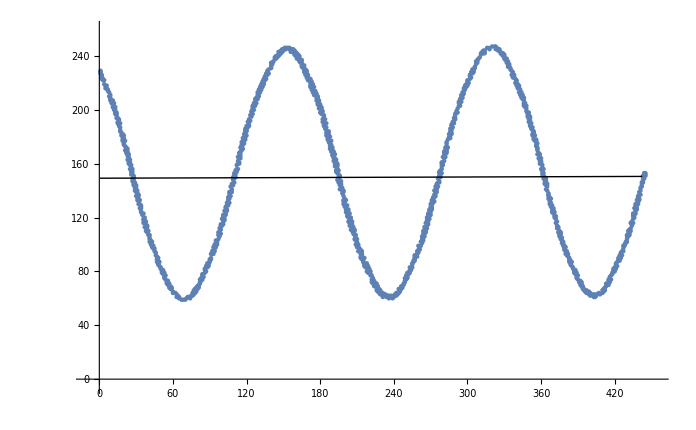

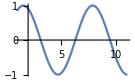

```mathematica
Table[Plot[Sin[n x],{x,1,11}],{n,1}]
```

```mathematica
poz=Position[{liste},1,153,1];
poz=Part[poz]⟦1,2⟧;
tepex2=SortBy[liste]⟦1,1,1⟧;
cukurx2=SortBy[liste]⟦1,poz,-1⟧;
Print[tepex2]
Print[cukurx2]
Print[poz]
```